## Damped Pendulum — With Animated Graphics — SOLVED

## Started in class, February 7, 2025, and you are finishing as Problem Set 6 for February 11.

#### General Second-Order Runge-Kutta — Implementation

The implementation of the damped pendulum is almost the same as the damped oscillator. Figure out what needs to be changed.

```mathematica
lambda=1;
rungeKutta2[cc_]:=(
(* Extract time, angle, and angular velocity from the list *)
curTime=cc[[1]];
curAngle=cc[[2]];
curAngularVelocity=cc[[3]];
(* Compute tStar, xStar, vStar *)
tStar=curTime + lambda deltaT;
thetaStar=curAngle+curAngularVelocity lambda deltaT;
omegaStar=curAngularVelocity+α[curTime,curAngle,curAngularVelocity]lambda deltaT;
(* Implement General Second-Order Runge-Kutta *)
newTime=curTime+deltaT;
newAngularVelocity=curAngularVelocity+((1-1/(2lambda))α[curTime,curAngle,curAngularVelocity]+1/(2lambda)α[tStar,thetaStar,omegaStar])deltaT;
newAngle=curAngle+(curAngularVelocity+newAngularVelocity)deltaT/2;
{newTime, newAngle, newAngularVelocity}
)
N[rungeKutta2[initialConditions]] (* Test the rungeKutta2 function you just wrote. *)
(* The output just below should be {0.0025,0.174531,-0.00694977} *)
```

#### Drawing a Pendulum with Coordinates and Graphics

To do a legible job of this, you may need to review Section 14 of EIWL3. The goal is to finish implementing the function below so that you get a picture something like the one I have pasted in.

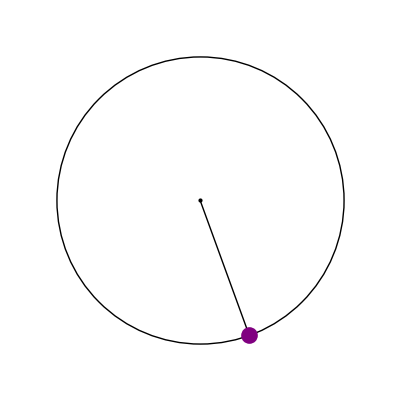

```mathematica
pendulumGraphic[angle_]:=Graphics[{
EdgeForm[Thin],White,
RegularPolygon[{0.0,0.0},0.4,4],
Black,
Circle[{0,0},length],
(* all I left for you to add is two points and a line *)
Point[{0,0}],
Line[{{0,0},length{ Sin[angle],- Cos[angle]}}],
PointSize[0.03], Purple,(* This directive affects any remaining items in the list *)
Point[length{ Sin[angle],- Cos[angle]}]
}]
pendulumGraphic[20°]
```

The pendulum graphic you are trying for (when the function is passed in 20.ba for the angle, and of course your function should do the right thing for any other angle):

-Graphics-